```mathematica
Clear["Global`*"]
```

Variables to Adjust

```mathematica
Coordinates :={-308,311,-299,275,-240,196,-147,99,-58,28,-10,2}
```

```mathematica
P:=11
```

```mathematica
Valuation:=2
```

END of Variables to Adjust

```mathematica
XMax := 20
```

```mathematica
XOffset:=0
```

```mathematica
SumOfBinomials[vector_,x_] := Sum[vector[[i+1]]*Binomial[x,i],{i,0,Length[vector]-1}]
```

```mathematica
ValuationInteger[p_,x_] :=If[!Divisible[x,p],0,ValuationInteger[p,x/p]+1]
```

```mathematica
ValuationRational[p_,x_] := If[Divisible[Numerator[x],p],ValuationInteger[p,Numerator[x]],-ValuationInteger[p,Denominator[x]]]
```

```mathematica
Poly[x_]=Expand[InterpolatingPolynomial[Table[SumOfBinomials[Coordinates,x+XOffset],{x,1,20}],x]]
```

-308+(9723517 x)/13860-(431909 x^2)/720+(123702589 x^3)/453600-(2738635 x^4)/36288+(4934567 x^5)/362880-(14251 x^6)/8640+(9139 x^7)/67200-(13 x^8)/1728+(97 x^9)/362880-x^10/181440+x^11/19958400

```mathematica
FixedPointPoly[x_] = Poly[x] - x
```

-308+(9709657 x)/13860-(431909 x^2)/720+(123702589 x^3)/453600-(2738635 x^4)/36288+(4934567 x^5)/362880-(14251 x^6)/8640+(9139 x^7)/67200-(13 x^8)/1728+(97 x^9)/362880-x^10/181440+x^11/19958400

```mathematica
NewtonPlot[p_,polynomial_]:=ListLinePlot[Table[ValuationRational[p,x],{x,CoefficientList[polynomial[x],{x}]}],AxesOrigin->{0,0},GridLines->{{},Range[-100,100]},PlotMarkers->All,DataRange->{0,Length[CoefficientList[polynomial[x],{x}]]-1},PlotLabel->"p = "<>ToString[p],PlotRange->All,AspectRatio->Automatic]
```

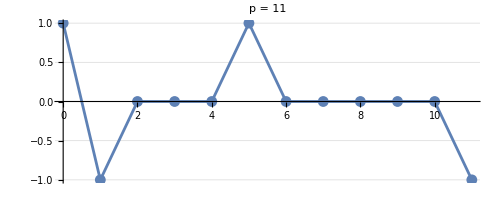

```mathematica
NewtonPlot[P,FixedPointPoly]
```

## To check for definitely bad reduction: Set Valuation to the negative of the steepest slope in the NewtonPlot.

```mathematica
Adjustment = Table[Valuation*x,{x,0,Length[CoefficientList[Poly'[x],{x}]]-1}]
```

{0,2,4,6,8,10,12,14,16,18,20}

```mathematica
FixedPointDerivativeValn=Table[ValuationRational[P,x],{x,CoefficientList[Poly'[x],{x}]}] + Adjustment
```

{-1,2,4,6,9,10,12,14,16,18,20}

```mathematica
UniqueMinimum:=Count[FixedPointDerivativeValn,Min[FixedPointDerivativeValn]]==1
```

```mathematica
NegativeMinimum:=Min[FixedPointDerivativeValn]<0
```

### If this value is true, then we have definitely bad reduction.

```mathematica
And[UniqueMinimum,NegativeMinimum]
```

True

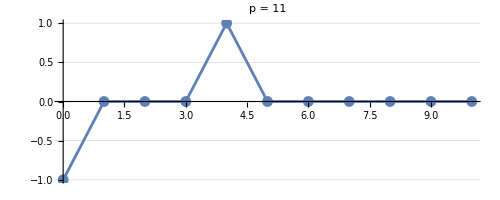

```mathematica
NewtonPlot[P,Poly']
```